```mathematica
Get["C:\\Users\\douwm\\repos\\wolfram_summer_school\\2d_toolbox.wl"]
```

```mathematica
nfreepoints = 8;
nunknowns = nfreepoints*2;
symtriagworm =MakeSymbolicTriangleWorm[{0,0},{1,0},nfreepoints];
endeffector = symtriagworm[[-1]];
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{32.6735,{len1→0.625444,len2→0.951317,len3→0.642926,len4→0.837942,len5→0.695891,len6→0.98124,len7→0.620334,len8→0.620888,len9→0.963168,len10→0.962698,len11→0.616662,len12→0.613816,len13→0.983414,len14→0.611386,len15→0.983022,len16→0.633138}}

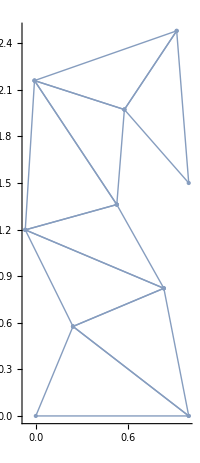

```mathematica
minlen = 0.6;
maxlen = 1;
desired = {1,1.5};
endeffectorconstraints:= {Norm[endeffector-desired]};
rodlengthconstraint=MakeLengthConstraints[nunknowns,minlen,maxlen];
constraints = Join[endeffectorconstraints,rodlengthconstraint];
AbsoluteTiming[
sol = OptForDesired[constraints,MakeOptStartPoint[nunknowns]]]
MeshAllTriag[symtriagworm/.sol,Automatic]
(*
path = Table[{i,0.5*Sin[10*i]+2.5},{i,0.7,2.2,0.01}];
pathsol = SolveForPath[path,nunknowns];
*)
```

```mathematica
AbsoluteTiming[
sol = OptForDesiredWithGrad[constraints,MakeOptStartPoint[nunknowns]]]
```

{0.0000962,OptForDesiredWithGrad[{√(Abs[-1+4+len15 Cos[ArcCos[1]+1]]^2+Abs[-1.5+4+len15 1]^2),0.6<len1<1,13,0.6<len15<1,0.6<len16<1},{1}]}
 |  |  |  |

```mathematica
?OptForDesiredWithGrad
```

```mathematica
Plot3D[ThirdCoord[{0,0},{0,1.1},l1,l2],{l1,0.6,1},{l2,0.6,1}]
```

-Graphics3D-

Numerical optimisation

```mathematica
desired = {1,2}
Cost[lengths_]:=Norm[MakeTriangleWorm[{0,0},{1,0}, lengths][[-1]] - desired];
vars = Table[Unique["n"],18];
startloc = Thread[{vars,1}];
AbsoluteTiming[FindMinimum[Cost[vars], startloc];]
```

{1,2}

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{31.5223,Null}